```mathematica
Solve[a x^2+b x + c == 0 /. x-> (2c)/(√(b^2-4a c)-b)]
```

{{}}

{{x→1.77939,y→0.494336},{x→0.494336,y→1.77939},{x→0.604719-1.38415 ⅈ,y→-0.99158+0.115464 ⅈ},{x→0.604719+1.38415 ⅈ,y→-0.99158-0.115464 ⅈ},{x→-0.99158+0.115464 ⅈ,y→0.604719-1.38415 ⅈ},{x→-0.99158-0.115464 ⅈ,y→0.604719+1.38415 ⅈ}}

{{1.77939,0.494336},{0.494336,1.77939}}

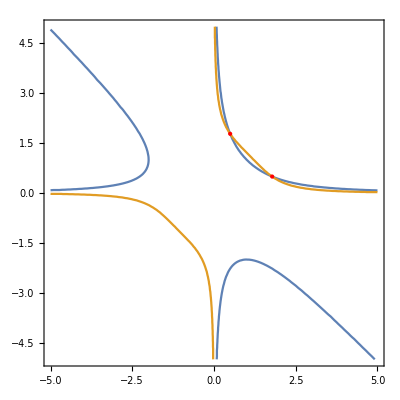

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

```mathematica
eq1 = x^2 * y + x * y^2 -2 == 0;
eq2 = x^3 * y + x * y^3 - 3== 0;
sol = NSolve[{eq1,eq2},{x,y}]
Select[{x,y}/.sol,#[[1]]∈Reals&]
ContourPlot[{x^2 * y + x * y^2 - 2 == 0, x^3 * y + x * y^3 - 3== 0},{x,-5,5},{y,-5,5},Epilog->{PointSize[Large],Red,Point[Select[{x,y}/.sol,#[[1]]∈Reals&]]}]
```

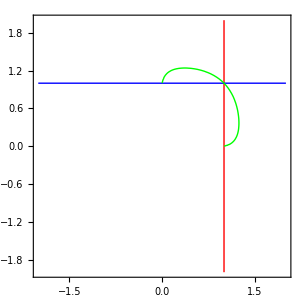

```mathematica
ContourPlot[{x==1,y==1, x^x+y^y-2==0},{x,-2,2},{y,-2,2},ContourStyle ->{{Red,Thick},{Blue,Thick},{Green,Thick}},Epilog->{PointSize[Large],Green}]
```

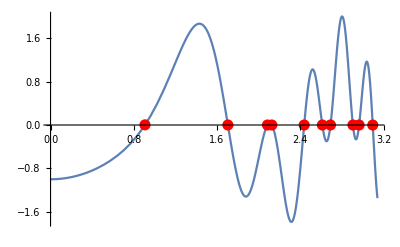

```mathematica
f[x_]:= Sin[x^2] - Cos[x^3];
Plot[f[x],{x,0, Pi},Mesh->{{0}},MeshFunctions->(f[#]&),MeshStyle->Directive[PointSize[0.02],Red]]
```

```mathematica
f[x_, y_] := 2 * x * y^4 + x^2 * y^3 - 2 * x^3 * y^2 - y^5 - x^4 * y + 2 * y;
FindInstance[{f[x,y]==Fibonacci[10],x>0,y>0},{x,y},Integers]
Fibonacci[10]
f[34,55]
```

{{x→34,y→55}}

55

55

```mathematica
Subscript[A_,n_]:=Table[x^(Abs[i-j]+i*j),{i,1,n},{j,1,n}]
discriminant3 = Simplify[Det[Subscript[A,3]]^2,Assumptions->x>0];
Solve[discriminant3==0,x];
discriminant4=Simplify[Det[Subscript[A,4]]^2,Assumptions->x>0];
Solve[discriminant4==0,x];
det6=Simplify[Det[Subscript[A,6]]==0,Assumptions->x>0];
xValues=x/. Solve[det6,x];
Union[xValues];
```